## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[23]
```

{23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

## Topic

### Definition / Theorem

This is text.

#### Example

## Gamma Function( TBD: ALERT )

```mathematica
ClearAll[gamma]
(*gamma[s_]:=Integrate[x^(s-1)ⅇ^-x,{x,0,Infinity}]*)
gamma[x_]:=Integrate[t^(x-1)ⅇ^-t,{t,0,Infinity},Assumptions->{Re[t]>1}]
gamma2[x_]:=1/x Integrate[t^x ⅇ^-t,{t,0,Infinity}]
Log[10.,Gamma[70]]
```

98.2333

2.54926

2.54926

120

2.54926

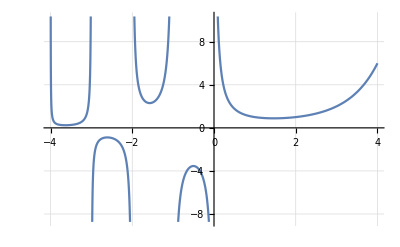

```mathematica
gamma[3.25]//N
gamma2[3.25]//N
gamma[6]
Gamma[3.25]//N
Plot[Gamma[x],{x,-4,4},GridLines->Automatic]
```

```mathematica
gamma[z_]:=Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]
gamma[z]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[t^(z-1)-ⅇ^-t,{t,0,Infinity}]+Integrate[ⅇ^-t(z-1)t^(z-2),{t,0,Infinity}]
```

Integrate::idiv: Integral of -ⅇ^-t+t^(-1+z) does not converge on {0,∞}.

ConditionalExpression[Gamma[z]+∫_0^∞ (-ⅇ^-t+t^(-1+z))ⅆt, Re[z]>1]

```mathematica
1/6-5/66
```

1/11

```mathematica
D[ -x Cos[x]+Sin[x],{x,1}]//FullSimplify
```

x Sin[x]

```mathematica
Integrate[Gamma[z],z]
```

∫Gamma[z]ⅆz

```mathematica
Integrate[Exp[-a u^2],{u,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √a), Re[a]>0]

```mathematica
Integrate[ⅇ^((z-1)Log[t]-t),{t,0,Infinity}]
```

ConditionalExpression[Gamma[z], Re[z]>0]

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
Gamma[I]//N
```

-0.15495-0.498016 ⅈ

```mathematica
Integrate[t^(z-1)ⅇ^-t,{t,0,Infinity}]/.z:>5
```

24

```mathematica
u[t_]:=t^(z-1)
u[t_]:=1
v[t_]:=-ⅇ^-t
```

```mathematica
Integrate[u[t]D[v[t],{t,1}],{t,0,Infinity}]

Integrate[v[t]D[u[t],{t,1}],{t,0,Infinity}]
```

1

0

```mathematica
Integrate[x ⅇ^(5x),x]
```

ⅇ^(5 x) (-1/25+x/5)

```mathematica
D[ⅇ^-t t^(x-1),{x,3}]
```

```mathematica
Gamma'''[x]
Integrate[ⅇ^-t t^(-1+x) Log[t]^3,{x,0,Infinity}]
```

Gamma[x] PolyGamma[0,x]^3+3 Gamma[x] PolyGamma[0,x] PolyGamma[1,x]+Gamma[x] PolyGamma[2,x]

ConditionalExpression[-(ⅇ^-t Log[t]^2)/t, Re[Log[t]]<0]

```mathematica
240*.35
```

84.

```mathematica
Solve[{Gamma'[x]==1},x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Gamma[x] PolyGamma[0,x]==1},x]

```mathematica
f[y_]:=Integrate[x Cos[x],x]/.x:>y
f[π]-f[0]
```

-2

```mathematica
Integrate[x Cos[x],{x,0,π}]
```

-2

```mathematica
Table[Residue[Gamma[z],{z,-k}],{k,1,7}]
```

{-1,1/2,-1/6,1/24,-1/120,1/720,-1/5040}

```mathematica
1/(Gamma[z]Gamma[1-z])//FullSimplify
```

Sin[π z]/π

```mathematica
Series[Sin[π z]/π,{z,0,9}]
```

z-(π^2 z^3)/6+(π^4 z^5)/120-(π^6 z^7)/5040+(π^8 z^9)/362880+O[z]^10

```mathematica
Zeta[2];
Denominator[Zeta[6]]
5040/945
```

945

16/3

```mathematica
Zeta[4]
120/90
```

π^4/90

4/3

```mathematica
Zeta[8]
362880/9450
```

π^8/9450

192/5

```mathematica
Integrate[t^(n-1)ⅇ^-t,{t,0,Infinity},Assumptions->n >1 && Element[n,Integers]]
```

Gamma[n]

```mathematica
D[t^(n-1),{t,1}]
```

(-1+n) t^(-2+n)

```mathematica
g[n_]:=-(t^(n-1))ⅇ^-t
Limit[g[n]-g[0],n->Infinity]
```

ConditionalExpression[ⅇ^-t/t, (ⅇ^-t/t|ⅇ^-t)∈ℝ&&Log[t]<0]

```mathematica
Integrate[t^(1-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(2-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(3-1)ⅇ^-t,{t,0,Infinity}]
Integrate[t^(4-1)ⅇ^-t,{t,0,Infinity}]
```

1

1

2

6

```mathematica
Integrate[t^4 ⅇ^-t,{t,0,Infinity}]
```

24

```mathematica
Limit[(-m ⅇ^-m+1),m->Infinity]
```

1

```mathematica
Product[(2k 2k)/((2k-1)(2k+1)) ,{k,1,Infinity}]
```

π/2

```mathematica
Gamma'[z]/Gamma[z]
```

PolyGamma[0,z]

```mathematica
Series[PolyGamma[0,z],{z,0,6}]
```

-1/z-EulerGamma+(π^2 z)/6+1/2 PolyGamma[2,1] z^2+(π^4 z^3)/90+1/24 PolyGamma[4,1] z^4+(π^6 z^5)/945+1/720 PolyGamma[6,1] z^6+O[z]^7

```mathematica
Series[PolyGamma[1,z],{z,0,6}]
```

1/z^2+π^2/6+PolyGamma[2,1] z+(π^4 z^2)/30+1/6 PolyGamma[4,1] z^3+(π^6 z^4)/189+1/120 PolyGamma[6,1] z^5+(π^8 z^6)/1350+O[z]^7

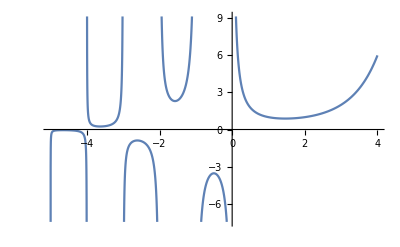

```mathematica
Plot[Gamma[x],{x,-5,4}]
```

```mathematica
Table[{k,Residue[Gamma[z],{z,-k}]},{k,1,7}]//TableForm
```

1 | -1
2 | 1/2
3 | -1/6
4 | 1/24
5 | -1/120
6 | 1/720
7 | -1/5040

```mathematica
g[n_]:=Product[(1+1/k)^n/(1+n/k),{k,1,Infinity}]
```

```mathematica
g[4]
```

24

```mathematica
π^2/6//N
```

1.64493

```mathematica
Integrate[1/x^2,{x,1,Infinity}]
```

1

```mathematica
Sum[1/k^2,{k,1,Infinity}]//N
```

1.64493

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2
9 | 2
10 | 4
11 | 2
12 | 4

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,101,111}]//tf
```

101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

## Prime Distribution

### Prime-counting function π(x)

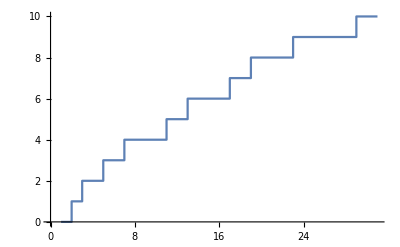

```mathematica
ListStepPlot[Table[{n,PrimePi[n]},{n,30}]]
```

```mathematica
Table[{n,PrimePi[n]},{n,10}]
```

{{1,0},{2,1},{3,2},{4,2},{5,3},{6,3},{7,4},{8,4},{9,4},{10,4}}

```mathematica
primePi2[n_]:=If[n==1,Log[2Pi],If[PrimePowerQ[n],Log[FactorInteger[n][[1,1]]],0]]
Table[primePi2[n],{n,12}]
```

{Log[2 π],Log[2],Log[3],Log[2],Log[5],0,Log[7],Log[2],Log[3],0,Log[11],0}

### Prime-counting function J(x)

```mathematica
heavysideTheta[x_]:=If[x==0,1,HeavisideTheta[x]]
plist[x_]:=Table[y,{y,Select[Range[x],PrimeQ]}]
```

```mathematica
j1[y_]:=Sum[1/n PrimePi[y^(1/n)],{n,1,Ceiling[Log[y]/Log[2]]}]
j2[x_]:=Sum[Sum[1/n heavysideTheta[(x-p^n)],{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p[y_]:=Table[1/n PrimePi[y^(1/n)],{n,1,Ceiling[Log[y]/Log[2]]}]
j2p[x_]:=Table[Table[1/n heavysideTheta[(x-p^n)],{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p2[y_]:=Table[{1/n,y^(1/n)//N,PrimePi[y^(1/n)]},{n,1,Ceiling[Log[y]/Log[2]]}]
j2p2[x_]:=Table[Table[{1/n,(x-p^n),1/n heavysideTheta[(x-p^n)]},{n,1,Ceiling[Log[x]/Log[2]]}],{p,plist[x]}]
```

```mathematica
j1p[11]//N
j2p[11]//N
```

{5.,1.,0.333333,0.}

{{1.,0.5,0.333333,0.},{1.,0.5,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.}}

### Stan Wagon Interpretation

```mathematica
pi0[x]:=1/2 (PrimePi[x+0.001]+PrimePi[x-0.001]);
```

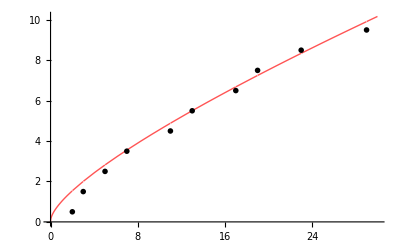

```mathematica
Plot[{RiemannR[x],pi0[x]},{x,0,30},PlotPoints->30,PlotStyle->{{Thick,Lighter[Red]},{Black,Thickness[0.004]}},Exclusions->(x==#&)/@Prime[Range[10]],Epilog->{PointSize[0.01],Point[Table[{Prime[i],i-1/2},{i,10}]]}]
```

```mathematica
rho=N[ZetaZero[Range[100]]];
muValues=Table[MoebiusMu[n]/n,{n,154}];
muIndices=Flatten[Position[muValues,_?(#!=0&)]];
mu=-2 muValues[[muIndices]];
T[x_,k_]:=mu.Re[ExpIntegralEi[(rho[[k]]Log[N[x]])/muIndices]]
Attributes[T]=Listable;
domain=Range[12.,100,88/200];
TData=Table[T[domain,i],{i,100}];
```

```mathematica
Manipulate[ListLinePlot[Transpose[{domain,TData[[i]]}],Frame->True,Axes->False,PlotStyle->Thick,PlotRange->{-0.5,0.5}],{i,1,100,1}]
```

```mathematica
RiemannData=RiemannR[domain]+1/π ArcTan[Pi/Log[domain]]-1/Log[domain];

TDataEnhanced=Table[Transpose[{domain,ss}],{ss,FoldList[Plus,RiemannData,TData]}];
```

```mathematica
pi0Plot=Plot[pi0[x],{x,0,100},PlotPoints->100,PlotStyle->{Red,Thickness[0.006]},Exclusions->(x==#&)/@Prime[Range[25]],Epilog->{PointSize[0.01],Red,Point[Table[{Prime[i],i-1/2},{i,25}]]}];
```

```mathematica
Manipulate[Show[pi0Plot,ListLinePlot[TDataEnhanced[[i]],PlotStyle->{Thickness[0.005],Blue}],Graphics[{PointSize[0.01],Table[Point[{Prime[i],i-1/2}],{i,25}]}],Ticks->{Range[20,100,10],Automatic},PlotRange->{{10,100},{5,27}},AxesOrigin->{10,5}],{i,1,50,1}]
```

```mathematica
Manipulate[Show[pi0Plot,ListLinePlot[TDataEnhanced[[i]],PlotStyle->{Thickness[0.005],Blue}],Graphics[{PointSize[0.01],Table[Point[{Prime[i],i-1/2}],{i,25}]}],Ticks->{Range[20,100,10],Automatic},PlotRange->{{10,100},{5,27}},AxesOrigin->{10,5}],{i,1,50,1}]
```

## Mellin Transformation

```mathematica
MellinTransform[2 ⅇ^-x,x,s]+MellinTransform[3 ⅇ^-x,x,s]//Simplify
MellinTransform[1/(ⅇ^x-1),x,s]
InverseMellinTransform[Gamma[s],s,x]
```

5 Gamma[s]

Gamma[s] Zeta[s]

ⅇ^-x

```mathematica
InverseMellinTransform[Gamma[s]Zeta[s],s,x]
```

1/(-1+ⅇ^x)

```mathematica
Sum[ⅇ^(-x n),{n,1,Infinity}]
```

1/(-1+ⅇ^x)

```mathematica
Integrate[x^(s-1)ⅇ^-x,{x,0,Infinity},Assumptions->{Re[s]>0}]
MellinTransform[ⅇ^-x,x,s]
InverseMellinTransform[Gamma[s],s,x]
1/(2π ⅈ)Integrate[x^-s Gamma[s],{s,-ⅈ Infinity,ⅈ Infinity}]
```

Gamma[s]

Gamma[s]

ⅇ^-x

```mathematica
1/(2π ⅈ)Integrate[x^-s Gamma[s],{s,1-ⅈ Infinity,1+ⅈ Infinity}]
```

-(ⅈ ∫_((-ⅈ) ∞)^(ⅈ ∞) x^-s Gamma[s]ⅆs)/(2 π)

```mathematica
DirichletTransform[DivisorSigma[0,n],n,s]
```

Zeta[s]^2

```mathematica
DirichletTransform[MangoldtLambda[n],n,s]
```

-Zeta'[s]/Zeta[s]

```mathematica
InverseMellinTransform[Zeta[s]^4/Zeta[2s],s,x]
```

InverseMellinTransform[Zeta[s]^4/Zeta[2 s],s,x]

## tmp-1

```mathematica
(-4 π^2)/7 Sum[Zeta[2k]/((2k+1)(2k+2)2^(2k)),{k,0,10}]//N
```

1.20206

```mathematica
Zeta[3]//N
```

1.20206

## tmp-2

```mathematica
(* Aantal (1,1) <= 100 *)
PrimePi[100/2]-1
PrimePi[100/3]-2
PrimePi[100/5]-3
PrimePi[100/7]-4
```

14

9

5

2

```mathematica
PrimePi[100/4]-1
PrimePi[100/9]
PrimePi[100/25]
```

8

5

2

```mathematica
Table[IntegerPartitions[k],{k,1,3}]//TableForm
```

1 |  | 
2 | 1
1 | 
3 | 2
1 | 1
1
1

## tmp-3

```mathematica
tstMa={{1,{{1}}},{2,{{2},{1,1}}},{3.{{3},{2,1},{1,1,1}}},{4},{5}};
tstMb={{1,{{1}}},{2,{{2},{1,1}}},{3,{{3},{2,1},{1,1,1}}}}
tstMc={{1,{{{1},10}}},{2,{{{2},20},{{1,1},30}}}}
tstM={{1,{{{1},{101}}}},{2,{{{2},{20}},{{1,1},{30}}}}}
(* Bouw db voor Report handmatig B.v. voor Levels 1-4; *)
```

{{1,{{1}}},{2,{{2},{1,1}}},{3,{{3},{2,1},{1,1,1}}}}

{{1,{{{1},10}}},{2,{{{2},20},{{1,1},30}}}}

{{1,{{{1},{101}}}},{2,{{{2},{20}},{{1,1},{30}}}}}

```mathematica
tM1={{"",1},{1,"."}};
tM2={{"",2,{1,1}},{2,".","."}};
tM3={{"",3,{2,1},{1,1,1}},{3,".",".","."}};
tM={tM1,tM2,tM3};

Grid[{
{Grid[tM1]},
{Grid[tM2]},
{Grid[tM3]}},Alignment->Left]

tM//Grid
tM//TableForm
```

| 1
1 | .
 | 2 | {1,1}
2 | . | .
 | 3 | {2,1} | {1,1,1}
3 | . | . | .

{,1} | {1,.}
{,2,{1,1}} | {2,.,.}
{,3,{2,1},{1,1,1}} | {3,.,.,.}

1 | 1
.
 | 
2 | 
1 | 1 | 2
.
.
 |  | 
3 |  | 
2 | 1 | 
1 | 1 | 1 | 3
.
.
.

```mathematica
-4 π^2 Zeta'[-2]//N
```

1.20206

## tmp-4

```mathematica
p:=Map[#->IntegerPartitions[#]&,Range[3]]//Association//Dataset
p;
f:=Map[#->FactorInteger[#]&,Range[10]]//Association//Dataset
f[[6]][[All,2]]
Map[#&,f][[All,2]][[10]]
```

```mathematica
p
f
```

```mathematica
Map[#[[All,2]]&,Dataset[Association[Map[#->FactorInteger[#]&,Range[10]]]]]
```

```mathematica
p:=Map[#->IntegerPartitions[#]&,Range[3]]//Association//Dataset
f:=Map[#[[All,2]]&,Dataset[Association[Map[#->FactorInteger[#]&,Range[10]]]]]
```

```mathematica
p
f
```

## tmp-5

### Pre-amble tmp-5

```mathematica
info:=<|1->{{1}->{2,3,5,7}},2->{{2}->{4,9},{1,1}->{6,10}},3->{{3}->{8},{2,1},{1,1,1}}|>//Association//Dataset
```

```mathematica
p:=Map[#->IntegerPartitions[#]&,Range[3]]//Association//Dataset
p
f:=Map[#->FactorInteger[#]&,Range[10]]//Association//Dataset
f
Map[#&,f][[All,2]][[10]];
Map[#&,f][[All,2]];
```

```mathematica
Map[#[[All,2]]&,Dataset[Association[Map[#->FactorInteger[#]&,Range[10]]]]]
```

```mathematica
inf2=info//Normal
```

<|1→{{1}→{2,3,5,7}},2→{{2}→{4,9},{1,1}→{6,10}},3→{{3}→{8},{2,1},{1,1,1}}|>

```mathematica
Head[inf2]
```

Association

```mathematica
Append[Append[Append[inf2[1;1][[1,2]],11],13],17]
```

{2,3,5,7,11,13,17}

### tmp 5.1 - Testing / Experimenting

```mathematica
Log[2π]//N
```

1.83788

```mathematica
NIntegrate[1/Log[t] 1/(t(t^2-1)),{t,ZetaZero[5],Infinity}]
```

-0.000101891+0.0000370054 ⅈ

```mathematica
DirichletTransform[MangoldtLambda[n],n,s]
```

-Zeta'[s]/Zeta[s]

```mathematica
1/131//N
```

0.00763359

```mathematica
InverseMellinTransform[Log[Zeta[s]]/s,s,x]
```

InverseMellinTransform[Log[Zeta[s]]/s,s,x]

```mathematica
MellinTransform[Floor[x],x,s]
```

MellinTransform[Floor[x],x,s]

```mathematica
DirichletTransform[(-1)^n,n,s]
```

-((1-2^(1-s)) Zeta[s])

```mathematica
Zeta[ZetaZero[115]]
```

0

```mathematica
DirichletEta[ZetaZero[3]]
```

0

```mathematica
DirichletTransform[MangoldtLambda[n],n,s]
```

-Zeta'[s]/Zeta[s]

## tmp-6

```mathematica
Log[Zeta[ZetaZero[100]]]
```

-∞

```mathematica
Log[0]
```

-∞

## tmp-7

### Stan Wagon Interpretation

```mathematica
pi0[x]:=1/2 (PrimePi[x+0.001]+PrimePi[x-0.001]);
```

```mathematica
Plot[{RiemannR[x],pi0[x]},{x,0,30},PlotPoints->30,PlotStyle->{{Thick,Lighter[Red]},{Black,Thickness[0.004]}},Exclusions->(x==#&)/@Prime[Range[10]],Epilog->{PointSize[0.01],Point[Table[{Prime[i],i-1/2},{i,10}]]}]
```

-Graphics-

```mathematica
rho=N[ZetaZero[Range[100]]];
muValues=Table[MoebiusMu[n]/n,{n,154}];
muIndices=Flatten[Position[muValues,_?(#!=0&)]];
mu=-2 muValues[[muIndices]];
T[x_,k_]:=mu.Re[ExpIntegralEi[(rho[[k]]Log[N[x]])/muIndices]]
Attributes[T]=Listable;
domain=Range[12.,100,88/200];
TData=Table[T[domain,i],{i,100}];
```

```mathematica
Manipulate[ListLinePlot[Transpose[{domain,TData[[i]]}],Frame->True,Axes->False,PlotStyle->Thick,PlotRange->{-0.5,0.5}],{i,1,100,1}]
```

```mathematica
RiemannData=RiemannR[domain]+1/π ArcTan[Pi/Log[domain]]-1/Log[domain];

TDataEnhanced=Table[Transpose[{domain,ss}],{ss,FoldList[Plus,RiemannData,TData]}];
```

```mathematica
pi0Plot=Plot[pi0[x],{x,0,100},PlotPoints->100,PlotStyle->{Red,Thickness[0.006]},Exclusions->(x==#&)/@Prime[Range[25]],Epilog->{PointSize[0.01],Red,Point[Table[{Prime[i],i-1/2},{i,25}]]}];
```

```mathematica
Manipulate[Show[pi0Plot,ListLinePlot[TDataEnhanced[[i]],PlotStyle->{Thickness[0.005],Blue}],Graphics[{PointSize[0.01],Table[Point[{Prime[i],i-1/2}],{i,25}]}],Ticks->{Range[20,100,10],Automatic},PlotRange->{{10,100},{5,27}},AxesOrigin->{10,5}],{i,1,50,1}]
```

```mathematica
Manipulate[Show[pi0Plot,ListLinePlot[TDataEnhanced[[i]],PlotStyle->{Thickness[0.005],Blue}],Graphics[{PointSize[0.01],Table[Point[{Prime[i],i-1/2}],{i,25}]}],Ticks->{Range[20,100,10],Automatic},PlotRange->{{10,100},{5,27}},AxesOrigin->{10,5}],{i,1,50,1}]
```

### Testing...

```mathematica
int[s]:=-Zeta'[s]/Zeta[s] x^s/s
```

```mathematica
Residue[int[s],{s,0}]
Residue[int[s],{s,1}]
```

-Log[2 π]

x

```mathematica
int[f[t]]
```

## tmp-8: ψ Function

### Step

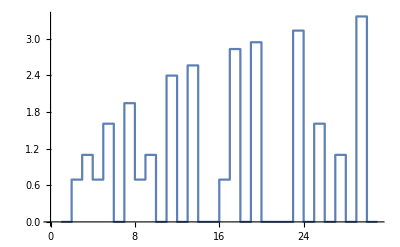

```mathematica
ListStepPlot[Table[{n,MangoldtLambda[n]},{n,30}]]
```

### Step Accumulate

```mathematica
Manipulate[
Show[{
ListStepPlot[
Partition[Riffle[Range[a],Simplify[Accumulate[Table[MangoldtLambda[n],{n,a}]]]],2],PlotStyle->{Black}],
Plot[x-Log[2Pi],{x,0,a},PlotStyle->{Blue,Dashed}]
}],
{{a,30},10,100,5},ControlPlacement->Bottom
]
```

### SmoothStep

[ TBD ]

```mathematica
1.
```

### Otherwise

```mathematica
g[z_]:=1/(z^3-3 z^2+2z)
cContourIntegral[g[z],z,{3,4I}]+cContourIntegral[g[z],z,{4I,-1}]+cContourIntegral[g[z],z,{-1,-4I}]+cContourIntegral[g[z],z,{-4I,3}]//N
```

-3.33067×10^-16+0. ⅈ

```mathematica
Residue[g[z],{z,2}]
Residue[g[z],{z,1}]
Residue[g[z],{z,0}]
```

1/2

-1

1/2

### Calculate Integral

```mathematica
h[z_]:=-Zeta'[z]/Zeta[z] x^z/z
```

```mathematica
int[a_,c_,t_]:=cContourIntegral[h[z],z,{c-I t,c+I t}]+cContourIntegral[h[z],z,{c+I t,a+I t}]+cContourIntegral[h[z],z,{a+ I t,a-I t}]+cContourIntegral[h[z],z,{a-I t,c-I t}]
int1[a_,c_,t_]:=cContourIntegral[h[z],z,{c-I t,c+I t}]
```

```mathematica
int1[a_,c_,t_]:=cContourIntegral[h[z],z,{c-I t,c+I t}]
int1[-1,2,14]//N
```

-((0.+28. ⅈ) x^s Zeta'[s])/(s Zeta[s])

```mathematica
int1[a_,c_,t_]:=cContourIntegral[h[z],z,{c-I t,c+I t}]
int2[a_,c_,t_]:=cContourIntegral[h[z],z,{c+I t,a+I t}]
int3[a_,c_,t_]:=cContourIntegral[h[z],z,{a+ I t,a-I t}]
int4[a_,c_,t_]:=cContourIntegral[h[z],z,{a-I t,c-I t}]
```

$Aborted

$Aborted

$Aborted

```mathematica
int1[-1,2,14]//N
```

```mathematica
NIntegrate[h[z],{z,2+13I,2+14I}]
```

NIntegrate::inumr: The integrand -(x^z Zeta'[z])/(z Zeta[z]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{2+13 ⅈ,2+14 ⅈ}}.

NIntegrate[h[z],{z,2+13 ⅈ,2+14 ⅈ}]

```mathematica
h[z_]:=-Zeta'[z]/Zeta[z] x^z/z
l[t_]:=(t-1)(-4+14I)+t(4+14I)
```

```mathematica
NIntegrate[h[l[t]]l'[t],{t,0,1}]
```

NIntegrate::inumr: The integrand -(28 ⅈ x^((-4+14 ⅈ) (-1+t)+(4+14 ⅈ) t) Zeta'[(-4+14 ⅈ) (-1+t)+(4+14 ⅈ) t])/(((-4+14 ⅈ) (-1+t)+(4+14 ⅈ) t) Zeta[(-4+14 ⅈ) (-1+t)+(4+14 ⅈ) t]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate[h[l[t]] l'[t],{t,0,1}]

```mathematica
PolynomialQ[2+x+1/x,x]
```

False

```mathematica
Zeta'[2]/Zeta[2]
```

(6 Zeta'[2])/π^2

```mathematica
Series[Zeta'[s],{s,0,1}]//Normal
```

-1/2 Log[2 π]+s (EulerGamma^2/2-π^2/24-1/2 (Log[2]+Log[π])^2+StieltjesGamma[1])

```mathematica
Integrate[-1/2 Log[2 π]+s (EulerGamma^2/2-π^2/24-1/2 (Log[2]+Log[π])^2+StieltjesGamma[1]),s]//FullSimplify//N
```

```mathematica
(0.020833333333333332 s (-7.619049607004975 s-22.054524796912144 (2.+1.8378770664093453 s)))/.s:>3
```

-11.7854

```mathematica
(Series[Zeta[s],{s,0,1}]//Normal//FullSimplify)/.s:>3//N
```

-3.25682

```mathematica
(1/2)/(1/3)
```

1.5

```mathematica
Sum[Zeta[-2k],{k,1,1}]//N
Sum[Zeta[-2k],{k,1,2}]//N
Sum[Zeta[-2k],{k,1,4}]//FullSimplify//N
Sum[Zeta[-2k],{k,1,8}]//FullSimplify//N
Sum[Zeta[-2k],{k,1,16}]//FullSimplify//N
Sum[Zeta[-2k],{k,1,32}]//FullSimplify//N
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Residue[h[z],{z,0}]
Residue[h[z],{z,1}]
Residue[h[z],{z,-2}]
Residue[h[z],{z,-4}]
Residue[h[z],{z,-6}]
Residue[h[z],{z,ZetaZero[1]}]+Residue[h[z],{z,1-ZetaZero[1]}]//Simplify//N//Simplify
Residue[h[z],{z,ZetaZero[2]}]+Residue[h[z],{z,1-ZetaZero[2]}]//Simplify//N//Simplify
```

-Log[2 π]

x

1/(2 x^2)

1/(4 x^4)

1/(6 x^6)

(-0.00249949-0.0706593 ⅈ) x^(0.5-14.1347 ⅈ)-(0.00249949-0.0706593 ⅈ) x^(0.5+14.1347 ⅈ)

(-0.00113077-0.0475422 ⅈ) x^(0.5-21.022 ⅈ)-(0.00113077-0.0475422 ⅈ) x^(0.5+21.022 ⅈ)

```mathematica
(Residue[h[z],{z,ZetaZero[2]}]/.x:>3//N)+
Residue[h[z],{z,1-ZetaZero[2]}]/.x:>3//N
```

0.148829+0. ⅈ

```mathematica
1/(0.5+14.1347I)//Simplify
```

0.0024995-0.0706595 ⅈ

```mathematica
Divisors[44100]
```

{1,2,3,4,5,6,7,9,10,12,14,15,18,20,21,25,28,30,35,36,42,45,49,50,60,63,70,75,84,90,98,100,105,126,140,147,150,175,180,196,210,225,245,252,294,300,315,350,420,441,450,490,525,588,630,700,735,882,900,980,1050,1225,1260,1470,1575,1764,2100,2205,2450,2940,3150,3675,4410,4900,6300,7350,8820,11025,14700,22050,44100}

```mathematica
FactorInteger[44101]
```

{{44101,1}}

```mathematica
FactorInteger[44089]
```

{{44089,1}}

```mathematica
er[44087]
```

{{44087,1}}

```mathematica
FactorInteger[44101]
```

{{44101,1}}

```mathematica
FactorInteger[213444]
```

{{2,2},{3,2},{7,2},{11,2}}

```mathematica
FactorInteger[213443]
```

{{461,1},{463,1}}

```mathematica
JacobiSymbol[13,5]
JacobiSymbol[13,9]
```

-1

1

```mathematica
Solve[x^2-63x + 992==0,x]
Solve[x^2-63x + 992==0,x,Modulus->3]
Solve[x^2-63x + 992==0,x,Modulus->15]
Solve[x^2-63x + 992==0,x,Modulus->30]
```

{{x→31},{x→32}}

{{x→1},{x→2}}

{{x→1},{x→2},{x→7},{x→11}}

{{x→1},{x→2},{x→7},{x→11},{x→16},{x→17},{x→22},{x→26}}

```mathematica
Solve[x^2-90x + 2021==0,x]
Solve[x^2-90x + 2021==0,x,Modulus->42]
```

{{x→43},{x→47}}

{{x→1},{x→5},{x→19},{x→29}}

```mathematica
210 48/210
EulerPhi[210]
Mod[101^48,210]
101^48
101 103
Solve[x^2-204x +10403==0,x]
Solve[x^2-204x + 10403==0,x,Modulus->(3 5 7 11 13)]
#[[1,2]]&/@Solve[x^2-204x + 10403==0,x,Modulus->(3 5 7 11 13)]//Length
```

48

48

1

1612226077682464366162063721580560437958839784543523124406943132996471824157105135854515307284801

10403

{{x→101},{x→103}}

{{x→101},{x→103},{x→376},{x→1258},{x→1531},{x→1676},{x→2378},{x→2831},{x→3106},{x→3533},{x→4261},{x→5108},{x→5381},{x→5953},{x→6263},{x→6536},{x→7108},{x→8111},{x→8683},{x→8956},{x→9266},{x→9838},{x→10111},{x→10958},{x→11686},{x→12113},{x→12388},{x→12841},{x→13543},{x→13688},{x→13961},{x→14843}}

32

```mathematica
Solve[x^2-64x +1024==0,x]
Solve[x^2-64x +1024==0,x,Modulus->33]
```

{{x→32},{x→32}}

{{x→32}}

```mathematica
f[x_]:=x^3+6x+7
Solve[f[x]==0,x,Modulus->(7 11 13 17)]
```

{{x→1121},{x→2430},{x→5796},{x→8414},{x→9723},{x→13089},{x→15520},{x→15707},{x→17016}}

```mathematica
13^5+3 13 +17
371349/31
```

371349

11979

```mathematica
f[x_]:=x^2+x+11
Solve[f[x]==0,x,Modulus->(3 7)]
```

{}

```mathematica
PowerMod[7,-1,13]
```

2

```mathematica
GCD[3,]
```

11

```mathematica
Solve[3x==144,x,Modulus->9]
```

{{x→1}}

```mathematica
105(2/3 4/5 6/7)
EulerPhi[105]
```

48

48

```mathematica
EulerPhi[15]
```

```mathematica
PartitionsP[2^20]
```

764586333769778521203376110491512432770144880429163734872796078672914050174391521829881949330057731872399258722796997727539506006682991399905510504251911238280594123670921276316913789805984156785761345187973783375368657098831335310677990647587571921859209504016505803949261041323276570577200576860584018747450828073121526608843474441940677028336892541601410861139521426585463087917686039862354078533160121874089112900138719141802375416944468347298182571206963131878870345997148908112956401751125480248978263327319664532043651431694289366772672204336215859807575759294952023104639544693154863610530587005228217001401984738846345689469779480390042882278724460175354868082276275239019400232594514918311955139278968453669200524375669937955135443971902073074853631220487757749482477012521303439275531705789797249024810354874355131909774772658451981900844473931996547800021385889966384050466043513680704721374553150997443853068597769561895762868724011010218389477861794177808399464980245041835692267620037112667771184253025701733770504895118836491711085810888102847915154831141440510936941633307907886352674492194788885875285525139544461000

```mathematica
EulerPhi[21]

Select[Table[k,{k,15}],GCD[15,#]==1&]
```

12

{1,2,4,7,8,11,13,14}

```mathematica
Select[Table[{k,FactorInteger[k],Mod[k,12]},{k,1,105}],GCD[#[[1]],105]==1&]//tf
```

1 | 1 | 1 | 1
2 | 2 | 1 | 2
4 | 2 | 2 | 4
8 | 2 | 3 | 8
11 | 11 | 1 | 11
13 | 13 | 1 | 1
16 | 2 | 4 | 4
17 | 17 | 1 | 5
19 | 19 | 1 | 7
22 | 2 | 1
11 | 1 | 10
23 | 23 | 1 | 11
26 | 2 | 1
13 | 1 | 2
29 | 29 | 1 | 5
31 | 31 | 1 | 7
32 | 2 | 5 | 8
34 | 2 | 1
17 | 1 | 10
37 | 37 | 1 | 1
38 | 2 | 1
19 | 1 | 2
41 | 41 | 1 | 5
43 | 43 | 1 | 7
44 | 2 | 2
11 | 1 | 8
46 | 2 | 1
23 | 1 | 10
47 | 47 | 1 | 11
52 | 2 | 2
13 | 1 | 4
53 | 53 | 1 | 5
58 | 2 | 1
29 | 1 | 10
59 | 59 | 1 | 11
61 | 61 | 1 | 1
62 | 2 | 1
31 | 1 | 2
64 | 2 | 6 | 4
67 | 67 | 1 | 7
68 | 2 | 2
17 | 1 | 8
71 | 71 | 1 | 11
73 | 73 | 1 | 1
74 | 2 | 1
37 | 1 | 2
76 | 2 | 2
19 | 1 | 4
79 | 79 | 1 | 7
82 | 2 | 1
41 | 1 | 10
83 | 83 | 1 | 11
86 | 2 | 1
43 | 1 | 2
88 | 2 | 3
11 | 1 | 4
89 | 89 | 1 | 5
92 | 2 | 2
23 | 1 | 8
94 | 2 | 1
47 | 1 | 10
97 | 97 | 1 | 1
101 | 101 | 1 | 5
103 | 103 | 1 | 7
104 | 2 | 3
13 | 1 | 8

```mathematica
Select[Table[{k,FactorInteger[k],Mod[k,12]},{k,1,105}],GCD[#[[1]],105]==1&]
```

{{1,{{1,1}},1},{2,{{2,1}},2},{4,{{2,2}},4},{8,{{2,3}},8},{11,{{11,1}},11},{13,{{13,1}},1},{16,{{2,4}},4},{17,{{17,1}},5},{19,{{19,1}},7},{22,{{2,1},{11,1}},10},{23,{{23,1}},11},{26,{{2,1},{13,1}},2},{29,{{29,1}},5},{31,{{31,1}},7},{32,{{2,5}},8},{34,{{2,1},{17,1}},10},{37,{{37,1}},1},{38,{{2,1},{19,1}},2},{41,{{41,1}},5},{43,{{43,1}},7},{44,{{2,2},{11,1}},8},{46,{{2,1},{23,1}},10},{47,{{47,1}},11},{52,{{2,2},{13,1}},4},{53,{{53,1}},5},{58,{{2,1},{29,1}},10},{59,{{59,1}},11},{61,{{61,1}},1},{62,{{2,1},{31,1}},2},{64,{{2,6}},4},{67,{{67,1}},7},{68,{{2,2},{17,1}},8},{71,{{71,1}},11},{73,{{73,1}},1},{74,{{2,1},{37,1}},2},{76,{{2,2},{19,1}},4},{79,{{79,1}},7},{82,{{2,1},{41,1}},10},{83,{{83,1}},11},{86,{{2,1},{43,1}},2},{88,{{2,3},{11,1}},4},{89,{{89,1}},5},{92,{{2,2},{23,1}},8},{94,{{2,1},{47,1}},10},{97,{{97,1}},1},{101,{{101,1}},5},{103,{{103,1}},7},{104,{{2,3},{13,1}},8}}

```mathematica
m=Select[Table[{k,FactorInteger[k],Mod[k,12]},{k,1,105}],GCD[#[[1]],105]==1&];
m=m[[All,3]]
GroupBy
```

{1,2,4,8,11,1,4,5,7,10,11,2,5,7,8,10,1,2,5,7,8,10,11,4,5,10,11,1,2,4,7,8,11,1,2,4,7,10,11,2,4,5,8,10,1,5,7,8}

```mathematica
ClearAll[m,n]

m=2;
n=1;

{(m^2-n^2),2 m n,(m^2+n^2)}
{(((m^2+n^2)+1)/2)^2-(((m^2+n^2)-1)/2)^2,2((m^2+n^2)+1)/2((m^2+n^2)-1)/2,(((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2}//Simplify
{(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2+1)/2)^2-(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2-1)/2)^2,2 (((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2+1)/2)(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2-1)/2),(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2+1)/2)^2+(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2-1)/2)^2}//Simplify
{(((((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2+1)/2)^2+(((((m^2+n^2)+1)/2)^2+(((m^2+n^2)-1)/2)^2-1)/2)^2+1)/2)^2,2}//Simplify
```

{3,4,5}

{5,12,13}

{13,84,85}

{1849,2}

```mathematica
ClearAll[m,n]
Table[{{(m^2-n^2),2 m n,(m^2+n^2)}},{m,2,20,2},{n,1}]//tf
```

3 | 4 | 5
15 | 8 | 17
35 | 12 | 37
63 | 16 | 65
99 | 20 | 101
143 | 24 | 145
195 | 28 | 197
255 | 32 | 257
323 | 36 | 325
399 | 40 | 401

```mathematica
399^2
40^2
401^2
```

159201

1600

160801